```mathematica
numbers = RandomReal[{-3,8},800]
```

{5.7756,-1.38956,2.52683,1.51145,-2.83167,1.78094,5.37656,0.0911494,5.45343,-2.87849,7.57293,4.97373,1.50665,5.41497,3.02604,5.3851,4.983,-2.95824,5.87203,0.347072,2.9288,-2.37517,0.35531,6.70635,-2.75203,-1.15696,-0.211985,5.33647,6.1127,-2.88659,5.30427,7.97028,1.07792,-0.914082,0.510086,5.65976,2.4457,4.01294,-1.27448,5.08174,0.113035,2.03568,2.36158,6.33745,7.99659,5.46043,3.65095,3.20991,5.42888,-0.13442,6.87371,4.19615,-2.81273,5.44812,-0.228052,2.78459,0.593372,6.83199,1.27979,7.11138,4.94574,6.7351,5.4793,6.26236,4.35826,4.9979,1.77594,4.074,4.27524,6.68321,7.58445,5.08046,4.61059,-0.84092,-0.934881,1.04134,7.43637,6.52197,-0.174351,-1.83566,-0.155197,3.22068,6.19422,0.659962,-2.47825,7.45954,0.363921,0.50197,6.76761,7.73869,6.54947,3.11279,2.65616,-1.13365,3.406,0.720006,0.0325666,0.890187,4.51944,-1.00419,2.69199,0.896968,6.95356,0.975355,0.172812,7.60489,0.457093,-2.88399,7.45746,-2.69096,1.05862,-2.77207,7.98841,-0.657313,-1.09049,4.57222,3.23629,7.94837,0.398642,-1.92214,-0.0131372,4.2788,-2.41093,1.90694,3.56542,6.01642,3.46625,5.55036,3.27558,0.816847,2.35786,2.15682,7.46936,2.73709,3.76742,5.08612,0.0300087,-1.20962,0.974457,0.730935,2.50222,2.89312,2.90995,3.78024,7.56495,5.59093,2.79496,-1.27527,1.21931,2.97092,-0.97006,3.6271,1.44972,-2.03065,1.78474,-2.4407,5.24643,0.832615,7.43141,0.354644,6.58454,3.46976,6.13287,1.72386,6.32288,7.26112,7.04994,3.41324,-2.01571,0.645623,6.38865,-0.622992,5.31703,3.55845,7.62321,3.84073,5.22951,-1.82923,2.83326,-2.95589,2.17022,5.30155,-1.69205,-0.94383,4.56007,-0.53698,5.6484,2.57683,3.23718,7.73188,0.132099,7.51698,3.20729,1.92816,0.153281,1.24771,3.99747,7.33935,-0.166628,6.38128,-1.05872,1.5345,5.4507,4.1536,-0.602422,4.4855,6.65822,6.11289,5.66853,2.23724,7.50179,4.02861,-0.920903,7.28994,-0.815453,0.249201,-0.130786,0.210524,-2.24424,7.41554,6.95588,3.42555,2.49913,-0.0814941,1.54896,6.2479,-1.96361,-1.88451,3.98001,6.24841,2.89865,-0.196227,-1.50871,2.65406,5.53215,0.477637,-0.627031,5.4173,7.99084,6.71777,3.09549,5.1328,0.593836,1.28793,1.79562,2.86606,3.8984,7.84999,2.18885,-1.53504,3.67989,-2.10495,3.02307,0.70739,5.03235,6.31055,-1.38926,6.09144,4.19675,7.34131,-0.656376,3.78542,5.30082,2.98695,7.55232,-2.91053,1.68425,7.65928,0.725072,-1.63952,0.672579,-0.501965,7.01306,7.42859,0.908526,-2.32224,-0.330334,7.61792,-0.535303,1.11095,4.02303,5.02173,0.108065,-1.43714,3.00328,-0.65117,1.77728,5.7469,-0.0604074,1.09492,5.34436,6.83889,0.614126,0.342057,-1.86907,-1.68024,-2.93519,5.24681,-1.54933,-2.37179,2.72969,-1.02807,7.52052,-1.3885,5.61712,2.10278,3.92722,5.05945,3.32865,7.25348,2.33145,-2.64503,5.26995,-0.271527,-0.0892168,0.0535416,0.673641,1.79409,3.70795,4.43244,-0.183929,5.3826,2.74995,-1.58246,3.47901,-0.199225,-1.47211,-0.0724246,-0.0547898,6.60464,5.37207,2.4238,2.17893,-2.70619,6.0773,-0.174685,-1.91498,-1.6814,-1.22062,-0.416431,6.45619,3.94464,3.91908,-1.41964,2.67275,2.10963,4.72155,-2.43256,-1.03757,-0.708101,5.72497,-0.873714,3.91427,7.11065,-0.648306,-1.03937,-0.0475979,6.6877,-2.25871,-0.462166,4.56801,7.89805,-1.83666,1.13798,-1.00606,4.75205,-2.21599,-1.30361,-1.44077,6.31245,-0.241324,6.99829,6.14601,-1.06069,-1.16619,-1.49618,7.13788,-2.57997,1.28313,5.33516,6.33597,2.98904,4.8174,0.63913,-1.48728,1.58002,3.76604,4.61712,2.64286,2.99683,-1.58349,0.278386,2.5732,7.43277,3.20624,5.54698,0.830066,3.83236,0.70329,6.24235,1.72226,3.62566,5.49714,3.89782,-1.32697,2.74128,3.90735,-2.76254,2.7736,6.40845,-0.0467941,1.96071,-1.28879,-0.0279566,1.30924,1.88627,-0.647967,7.92933,2.88789,7.0662,6.4218,-1.33821,0.369227,7.31044,-2.29746,3.88521,2.65427,5.83654,2.08511,4.9598,5.80049,-2.72455,1.4515,2.27693,-2.41727,3.54251,-0.835876,5.03563,3.53218,0.344082,7.75256,-0.295263,-1.1104,6.43297,2.64938,4.95805,2.15831,0.62298,-1.34476,-1.05713,0.964543,1.28542,2.019,6.79645,0.730546,2.28918,3.46173,-0.335665,7.08321,0.472256,7.11048,-0.500467,0.126055,4.50683,6.37972,1.13301,0.116578,5.54461,6.32156,-1.19039,6.64707,4.96578,4.39952,7.0737,0.500095,-1.83125,-2.7153,-0.865041,3.08157,0.947902,2.60724,2.91364,6.32564,0.0775214,7.27385,2.03312,1.35668,-0.827084,7.80701,1.0719,1.9664,-2.78096,5.89077,-1.66051,7.20644,-0.24985,7.86641,4.86775,2.98539,-1.689,3.99523,0.0264915,6.13231,2.9206,1.73112,0.960452,1.49828,7.95985,0.728995,3.93801,3.84851,4.18648,-1.7115,3.74446,0.0447347,6.62373,6.211,4.88619,7.87477,3.86672,0.306876,-2.73763,1.77197,3.67225,-1.05387,2.01013,5.11076,6.56842,4.37518,4.88917,1.12723,-1.40716,4.20742,6.50147,1.31639,4.58059,1.13183,7.23763,5.94735,0.946949,6.96602,7.0608,0.434779,-0.357252,2.96299,0.283005,3.66432,7.09911,2.74971,-2.66096,-2.01959,-1.08305,6.48058,0.865635,6.44981,5.23558,2.16681,6.22113,4.74786,-1.18253,-0.739316,2.61326,7.24071,2.69722,0.00167721,3.06654,3.86042,6.8749,6.43122,0.759505,3.50791,0.453637,0.125487,5.7053,1.78816,-2.97229,2.32293,4.98001,3.98625,-0.765436,-2.23685,7.2531,4.98841,6.11392,3.36899,-0.72114,3.21136,3.77597,6.90253,-0.663272,-2.67241,6.56582,4.39297,-0.330205,-2.8245,2.28912,2.70197,7.06678,7.85848,1.99332,-1.34221,-2.65255,-2.74266,4.34489,0.738533,4.74834,0.953702,3.34875,-0.656358,7.96174,7.39275,0.369046,-1.83195,6.64543,6.71893,0.0906922,-2.0283,7.12164,1.89529,5.32635,5.22207,-0.256114,0.342562,4.5283,2.86529,2.33583,4.4878,-1.48066,5.97136,4.48049,0.913954,5.81712,1.76798,6.06588,1.99191,0.833319,6.26603,5.0851,1.36547,-0.260959,5.11348,6.83773,7.74353,7.56836,7.96618,0.715619,5.61383,4.87586,-0.766155,-0.787613,6.15351,-1.2824,2.40098,3.74193,2.43762,0.910224,5.1123,7.32149,2.77203,-2.97002,5.39013,5.0858,3.14722,3.9638,4.37893,5.69716,6.21291,5.34017,5.41076,2.68919,3.00515,5.9914,-1.86887,7.93049,-1.14007,-1.19452,5.74529,-1.35945,5.85425,0.656831,-2.32527,3.69185,7.81724,4.15124,-0.239139,-0.448134,6.26595,6.78397,4.47332,0.00259062,1.02129,2.45388,2.48949,2.58691,2.45623,-2.1968,-0.0161274,7.68487,-1.44898,1.03016,5.66997,1.78714,7.6318,4.68102,7.30236,3.76181,0.515034,-1.49929,6.82788,-2.4805,6.83964,5.71701,-1.0504,3.91169,-0.782418,1.66756,-0.228651,7.87141,6.5412,7.27303,0.0784742,7.17081,0.173857,-0.771192,-0.986509,-0.442492,-2.82135,3.93776,-1.15348,6.34653,1.22157,-0.906793,0.529928,7.49488,0.370165,5.17155,-0.949038,-2.81601,3.04018,7.45735,1.60114,0.953625,6.11587,7.68893,3.51067,1.46159,-1.50523,-0.628138,4.13587,1.78811,-2.9657,-2.76722,6.93548,5.50654,-0.0797827,3.84882,-1.5692,2.92574,4.30256,5.38452,0.951179,5.84627,4.40418,4.88335,7.87524,-1.87581,2.48236,-0.751903,0.271216,3.86837,6.66636,7.69631,4.20696,-2.41834,7.78515,5.41403,-0.374431,-0.451903,7.38008,0.248294,-2.92309,6.76719,-2.41324,1.0326,6.65775,0.813148,-1.7319,2.45,7.32186,-2.67883,6.89482,-0.210759,3.30092,-1.89957,7.75133,-0.270586,-0.376899,-2.10549,3.6628,6.85249}

```mathematica
bins=BinCounts[numbers,{-3,8,1}]
```

{79,70,64,82,66,93,73,63,67,80,63}

```mathematica
Do[selectedNumbers=Select[numbers,i≤#<i+1&];
mean=Mean[selectedNumbers];
Print["Среднее значение для интервала [",i,";",i+1,"] = ",mean],{i,-3,7}]
```

Среднее значение для интервала [-3;-2] = -2.51288

Среднее значение для интервала [-2;-1] = -1.5414

Среднее значение для интервала [-1;0] = -0.459167

Среднее значение для интервала [0;1] = 0.583768

Среднее значение для интервала [1;2] = 1.52902

Среднее значение для интервала [2;3] = 2.51423

Среднее значение для интервала [3;4] = 3.49687

Среднее значение для интервала [4;5] = 4.4657

Среднее значение для интервала [5;6] = 5.47589

Среднее значение для интервала [6;7] = 6.53243

Среднее значение для интервала [7;8] = 7.43792

```mathematica
counts=Table[Count[numbers,i],{i,-3,8}]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

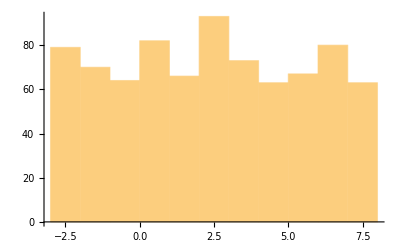

```mathematica
Histogram[numbers,11,PlotRange->{{-3,8},Automatic}]
```

```mathematica
Mean[numbers]
```

2.42685

```mathematica
(8+-3)/2
```

5/2

```mathematica
Variance[numbers]
```

9.83921

```mathematica
(8+3)^2/12//N
```

10.0833